# Finite Temperature Physics of Full Model

Isaac Wang

This notebook compute the finite temperature effective potential of the full model as well as the phase transition quantities.

```mathematica
$Assumptions={{μH,λ,μS,A,x1,x2,x3,h,v,w,mS,mh,θ,f,f-S,μHsq,μSsq}∈PositiveReals,{S,α,β}∈Reals,-π<=α<=π,-π<=β<=π};
MakeBoxes[μSsq,TraditionalForm]:="μ_S^2";
MakeBoxes[μHsq,TraditionalForm]:="μ_H^2";
MakeBoxes[x1,TraditionalForm]:="x_1";
MakeBoxes[x2,TraditionalForm]:="x_2";
MakeBoxes[x3,TraditionalForm]:="x_3";
MakeBoxes[mh,TraditionalForm]:="m_h";
MakeBoxes[mS,TraditionalForm]:="m_S";
```

```mathematica
MSbardata=Import[NotebookDirectory[]<>"../model_setup/output/f_5_beta_pi10.csv"][[2;;]];
lfunc[mS_,sinθ_]:=Interpolation[MSbardata[[All,{1,2,3}]]][mS,sinθ];
Afunc[mS_,sinθ_]:=Interpolation[MSbardata[[All,{1,2,4}]]][mS,sinθ];
μHsqfunc[mS_,sinθ_]:=Interpolation[MSbardata[[All,{1,2,5}]]][mS,sinθ];
μSsqfunc[mS_,sinθ_]:=Interpolation[MSbardata[[All,{1,2,6}]]][mS,sinθ];
```

```mathematica
(*Parameter input and integral definition*)
mW=80.379;
mZ=91.1876;
mt=173.34;
αsmZ=0.1184;
g3mZ=√(4π αsmZ);
GF=1.1663787×10^-5;
vnum=(√2 GF)^(-1/2);
mhpole=125.13;
(*Define integrals. The scale is fixed to be mZ*)
A0[M_]:=M^2(1-Log[M^2/mZ^2]);
B0[p_,M1_,M2_]:=-NIntegrate[Log[(x M1^2+(1-x)M2^2-x(1-x)p^2)/mZ^2],{x,0,1}]
ytmZ=2(GF/(√2)mt^2)^(1/2)+mt/(√2 vnum^3(4π)^2)(-(mhpole^2-4 mt^2)B0[mt,mhpole,mt]+(mt^2(80 mW^2 mZ^2-64 mW^4-7 mZ^4)+40 mW^2 mZ^4-32 mW^4 mZ^2-17 mZ^6)/(9 mt^2 mZ^2)B0[mt,mt,mZ]+(mt^2 mW^2+mt^4-2 mW^4)/mt^2 B0[mt,0,mW]+((3 mhpole^2)/(mhpole^2-mW^2)+2 mW^2/mt^2+3 mW^2/(mW^2-mZ^2)-10)A0[mW]+(3 mW^2/(mW^2-mhpole^2)+1)A0[mhpole]+(36 mt^2 mZ^2-56 mW^2 mZ^2+64 mW^4-17 mZ^4)/(9 mt^2 mZ^2)A0[mt]+((3 mW^2)/(mZ^2-mW^2)+(32 mW^4-40 mW^2 mZ^2+17 mZ^4)/(9 mt^2 mZ^2)-3)A0[mZ]+mhpole^2/2-3 mt^2-9 mW^2+7 mZ^2/18+64 mW^4/(9 mZ^2))+mt/(√2 vnum (4π))αsmZ(-8 A0[mt]/mt^2-8/3)//Re;
g2mZ=2(√2 GF)^(1/2)mW+2 mW/((4π)^2 vnum^3)((mhpole^4/(6 mW^2)-2 mhpole^2/3+2 mW^2)B0[mW,mhpole,mW]+(-mt^4/mW^2-mt^2+2 mW^2)B0[mW,0,mt]+1/6(-48 mW^4/mZ^2+mZ^4/mW^2-68 mW^2+16 mZ^2)B0[mW,mW,mZ]+1/6(mhpole^2(9/(mhpole^2-mW^2)+1/mW^2)+mZ^2/mW^2+mW^2(9/(mW^2-mZ^2)+48/mZ^2)-27)A0[mW]+(2-(mhpole^2(mhpole^2+8 mW^2))/(6 mW^2(mhpole^2-mW^2)))A0[mhpole]+(mt^2/mW^2+1)A0[mt]+1/6(24 mW^2/mZ^2-mZ^2/mW^2+9 mW^2/(mZ^2-mW^2)-17)A0[mW]+1/36(-3 mhpole^2+18 mt^2+288 mW^4/mZ^2-374 mW^2-3 mZ^2))//Re;
g1mZ=2(√2 GF)^(1/2)√(mZ^2-mW^2)+(2 √(mZ^2-mW^2))/((4π)^2 vnum^3)((88/9-(124 mW^2)/(9 mZ^2)+(mhpole^2+34 mW^2)/(6(mZ^2-mW^2)))A0[mZ]+(mhpole^2-4 mW^2)/(2(mhpole^2-mW^2))A0[mhpole]+(-7/9-mt^2/(mZ^2-mW^2)+64 mW^2/(9 mZ^2))A0[mt]+(mhpole^4+2 mW^2(mW^2-15 mZ^2)+3 mhpole^2(2 mW^2+7 mZ^2))/(6(mhpole^2-mW^2)(mW^2-mZ^2))A0[mW]-(mt^4+mW^2 mt^2-2 mW^4)/(mW^2-mZ^2)B0[mW,0,mt]-(mhpole^4-4 mZ^2 mhpole^2+12 mZ^4)/(6(mW^2-mZ^2))B0[mZ,mhpole,mZ]+(mhpole^4-4 mW^2 mhpole^2+12 mW^4)/(6(mW^2-mZ^2))B0[mW,mhpole,mW]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mW^2-mZ^2))B0[mW,mW,mZ]+1/9(-23 mW^2+7 mt^2+17 mZ^2-(64 mt^2 mW^2)/mZ^2-(9 mW^2(mt^2-mW^2))/(mZ^2-mW^2))B0[mZ,mt,mt]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mZ^2-mW^2))B0[mZ,mW,mW]+1/36(576 mW^4/mZ^2-242 mW^2-3 mhpole^2+257 mZ^2+36 mW^2/(mZ^2-mW^2)+mt^2(82-256 mW^2/mZ^2)))//Re;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.23578+2.46616 ⅈ and 0.000298064 for the integral and error estimates.

## Effective Potential

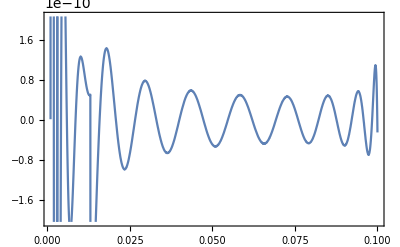

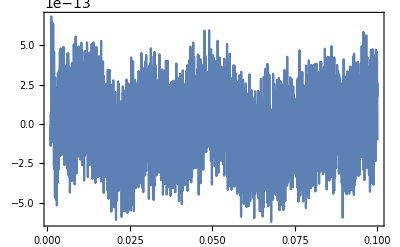

```mathematica
JB[x_]:=NIntegrate[z^2*Log[1-Exp[-Sqrt[z^2+x]]],{z,0,Infinity}]
(*bosonic field contributions*)
JF[x_]:=NIntegrate[z^2*Log[1+Exp[-Sqrt[z^2+x]]],{z,0,Infinity}]
(*fermionic field contributions*)
(*Cross check*)
fit11=Table[{ϕ,JB[ϕ]},{ϕ,10^(-1),200,.1}];
JBfit11[ϕ_]=Fit[fit11,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit12=Table[{ϕ,JB[ϕ]},{ϕ,10^(-3),10^(-1),10^(-3)}];
JBfit12[ϕ_]=Fit[fit12,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit13=Table[{ϕ,JB[ϕ]},{ϕ,0,10^(-3),10^(-6)}];
JBfit13[ϕ_]=Fit[fit13,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit21=Table[{ϕ,JF[ϕ]},{ϕ,10^(-1),200,.1}];
JFfit21[ϕ_]=Fit[fit21,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit22=Table[{ϕ,JF[ϕ]},{ϕ,10^(-3),10^(-1),10^(-3)}];
JFfit22[ϕ_]=Fit[fit22,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit23=Table[{ϕ,JF[ϕ]},{ϕ,0,10^(-3),10^(-6)}];
JFfit23[ϕ_]=Fit[fit23,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
JBfit[x_]:=JBfit11[x]/;10^(-1)<x≤200
JBfit[x_]:=JBfit12[x]/;10^(-3)<=x≤10^(-1)
JBfit[x_]:=JBfit13[x]/;0<=x≤10^(-3)
JBfit[x_]:=0/;200<x
JFfit[x_]:=JFfit21[x]/;10^(-1)<x≤200
JFfit[x_]:=JFfit22[x]/;10^(-3)<=x≤10^(-1)
JFfit[x_]:=JFfit23[x]/;0<=x≤10^(-3)
JFfit[x_]:=0/;200<x
Plot[{JBfit[x]-JB[x]},{x,10^(-3),10^(-1)}]
Plot[{JFfit[x]-JF[x]},{x,10^(-3),10^(-1)}]
```

```mathematica
V0[h_,S_]:=-1/2 μHsq h^2+1/4 λ h^4-1/2 A f (h^2-2 v^2)Sin[β+S/f]-f^2 μSsq (Cos[S/f]-1);
mWsq[h_]=1/4 g2mZ^2 h^2;
mZsq[h_]=1/4(g2mZ^2+g1mZ^2)h^2;
mtsq[h_]=1/2 ytmZ^2 h^2;
mWL[h_,T_]=1/4 g2mZ^2 h^2+11/6 g2mZ^2 T^2;
mgauge=({{g2mZ^2 x1^2/4+11/6 g2mZ^2 x2^2, -g2mZ g1mZ x1^2/4}, {-g2mZ g1mZ x1^2/4, g1mZ^2 x1^2/4+11/6 g1mZ^2 x2^2}});
gaugeL=Eigenvalues[mgauge]//FullSimplify;
mBL[h_,T_]=gaugeL[[1]]/.{x1->h,x2->T};
mZL[h_,T_]=gaugeL[[2]]/.{x1->h,x2->T};
(*VCW[h_,T_]:=1/(64 π^2)(4 mWsq[h]^2(Log[mWsq[h]/mZ^2]-1/2)+2 mZsq[h]^2(Log[mZsq[h]/mZ^2]-1/2)+2 mWL[h,T]^2(Log[mWL[h,T]/mZ^2]-3/2)+mZL[h,T]^2(Log[mZL[h,T]/mZ^2]-3/2)+mBL[h,T]^2(Log[mBL[h,T]/mZ^2]-3/2)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2));*)
VCW[h_]:=1/(64 π^2)(6 mWsq[h]^2(Log[mWsq[h]/mZ^2]-5/6)+3 mZsq[h]^2(Log[mZsq[h]/mZ^2]-5/6)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2));
V0T[h_,S_]:=V0[h,S]+VCW[h];
(*VFT[h_,T_]:=T^4/(2 π^2)(4JBBes[mWsq[h]/T^2]+2JBBes[mZsq[h]/T^2]+2JBBes[mWL[h,T]/T^2]+JBBes[mZL[h,T]/mZ^2]+JBBes[mBL[h,T]/mZ^2]-12JFBes[mtsq[h]/T^2]);*)
VFT[h_,T_]:=T^4/(2 π^2)(6JBfit[mWsq[h]/T^2]+3JBfit[mZsq[h]/T^2]-12JFfit[mtsq[h]/T^2]);
Vtot[h_,S_,T_]:=V0[h,S]+VCW[h]+VFT[h,T];
Spath[h_]:=f ArcTan[(A (h^2-2 v^2)Cos[β])/(2f μSsq+A (h^2-2 v^2)Sin[β])];
```

## Benchmark

```mathematica
num={λ->lfunc[5,0.16],A->Afunc[5,0.16],f->10^5,β->π/10,μHsq->μHsqfunc[5,0.16],μSsq->μSsqfunc[5,0.16],v->vnum/(√2)}
```

{λ→0.147575,A→10.5436,f→100000,β→π/10,μ_H^2→-317165.,μ_S^2→425.192,v→174.104}

```mathematica
V0Tnum[h_,S_]=V0T[h,S]/.num;
Vtotnum[h_,S_,T_]=Vtot[h,S,T]/.num;
Spathnum[h_]=Spath[h]/.num;
V0T1d[h_]:=V0Tnum[h,Spathnum[h]];
Vtot1d[h_,T_]:=Vtotnum[h,Spathnum[h],T]
```

```mathematica
Spathnum[vnum]
```

8.57965×10^-14

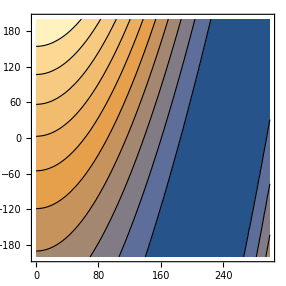

```mathematica
ContourPlot[V0Tnum[h,S],{h,0,300},{S,-200,200},Contours->10]
```

```mathematica
FindRoot[D[V0Tnum[h,S],{{h,S}}]==0,{{h,vnum},{S,0}}]
```

{h→246.22,S→-4.62833×10^-11}

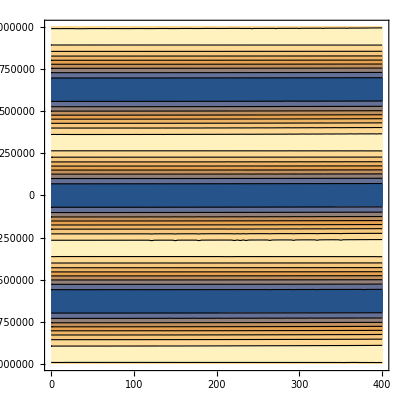

```mathematica
ContourPlot[V0Tnum[h,S],{h,0,400},{S,-10^6,10^6}]
```

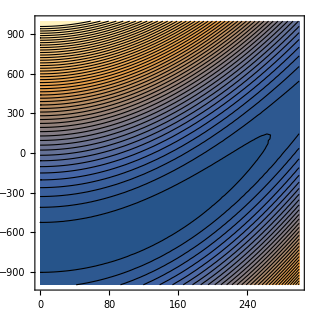

```mathematica
ContourPlot[Vtotnum[h,S,66.9],{h,0,300},{S,-1000,1000},Contours->50]
```

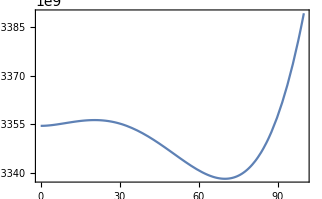

```mathematica
Plot[Vtotnum[h,Spathnum[h],67.3],{h,0,100}]
```